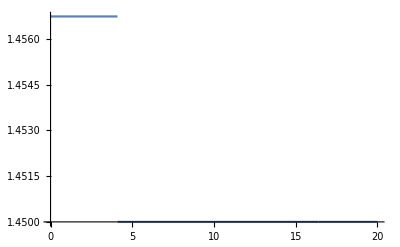

```mathematica
Clear["Global`*"]

dCore=8.2;
NA=0.14;
λ=1.55;
nMat=1.45;
β0=2Pi nMat/λ;

CalcWindow=20;(*mkm*)
N0=255;
h=0.01;

n[r_]:=Piecewise[{{Sqrt[nMat^2+NA^2],0≤r<dCore/2},{nMat,dCore/2≤r<2dCore},{Sqrt[nMat^2-0.0005I],2dCore≤r}}]

Plot[Re[n[r]],{r,0,CalcWindow}]
```

```mathematica
nArr=Array[n[Sqrt[#1^2+#2^2]]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
StartBeam=Array[Piecewise[{{1,0≤(#1^2+#2^2)<(dCore/2)^2},{0,(dCore/2)^2≤(#1^2+#2^2)}}]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];

D2Fourier=(Pi/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp=Exp[I/β0/2 D2Fourier h];
SpatialOp=Exp[-I/2/β0 (2 Pi/λ)^2 (nArr^2-nMat^2) h];
```

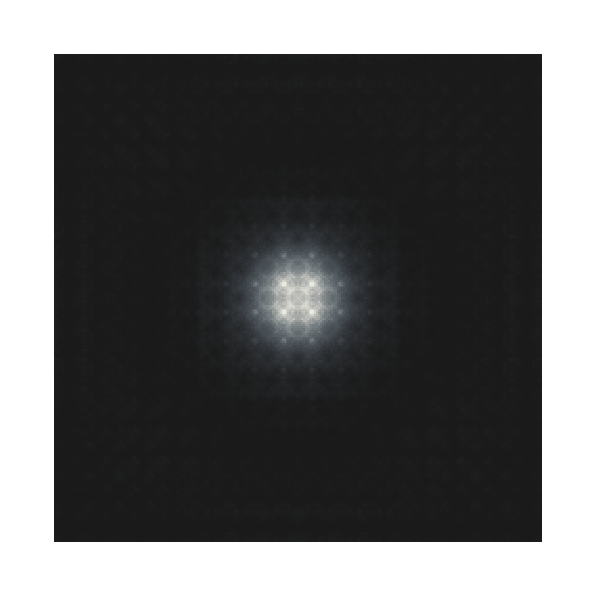

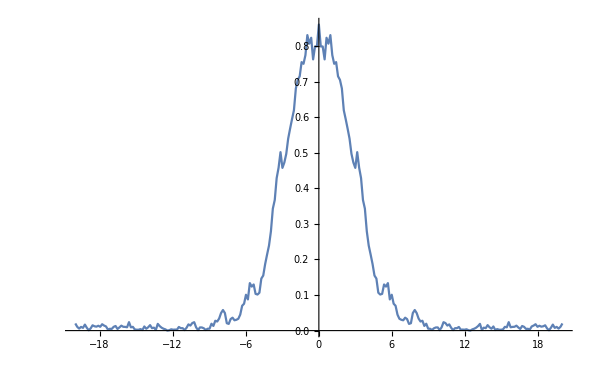

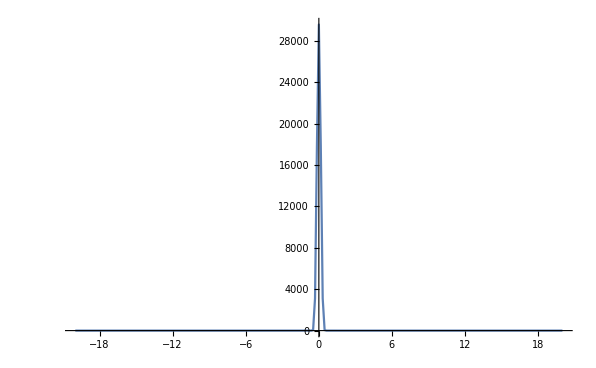

```mathematica
Beam=InverseFourier[Sqrt[FourierOp]Fourier[StartBeam]];
L=10000h;
Monitor[
For[ξ=0,ξ<L,ξ+=h,

Beam=InverseFourier[FourierOp Fourier[Beam SpatialOp]];

],{Round[(100 ξ)/L],ListPlot[Abs[Beam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{{-20,20},All},ImageSize->Medium]}]
Beam=InverseFourier[Fourier[Beam]/Sqrt[FourierOp]];

ArrayPlot[Abs[Beam]^2,DataRange->All,ColorFunction->"GrayTones"]

ListPlot[Abs[Beam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All}]
ListPlot[Abs[RotateRight[Abs[Fourier[Beam]]^2,{(N0-1)/2,(N0-1)/2}][[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All}]
```

Домашнее задание
1) Найти установившийся пучок в волокне (моду). Параметры волокна приведены в задаче. Подобрать оптимальный шаг дискретизации по z, по пространству и по Фурье-пространству для обеспечения приемлемой сходимости метода.
2) Сделать оператор идеальной тонкой линзы.
3) Ввести в однородную среду гауссовский пучок. Замоделировать его прохождение по такой среде. Сравнить с теоретической зависимостью.
4) Замоделировать “mode cleaner” или “spatial filter”. Объяснить как он работает и почему. На входе - гауссов пучок с гауссовым шумом, линзы - тонкие.
-Graphics-
5)* Замоделировать следующую задачу: к выходному волокну (SMF-28) приварена наварка (однородный непокрытый кварцевый цилиндр) диаметром 30 мкм длины L.
Построить график распределения интенсивности в пучке на выходе из наварки.
Построить график распределения интенсивности дифрагированного излучения в дальней зоне.
Вычислить M2 параметр качества пучка. Выбрать один из 2х способов измерения М2. 
	а) Прямой способ измерения M2 - посчитать моменты пучка по формулам из статьи Javier Alda - Laser and Gaussian Beam Propagation and Transformation. 
	б) Физический способ - поставить идеальную линзу на выходе излучения. Измерить диаметр перетяжки и расходимость. Вспомнить связь пространственного спектра и дифракции, для этого сообразить как 	перевести k_x в θ.

Оценить длину наварки L, при которой M2 портится в два раза.